Exercise 1
PART A)

```mathematica
V=30;
th=50*Pi/180;
g=9.8; (*grav. constant*)
l=0.5; (*length of pendulum*)
c=0.5;
m=200;
vt= 100;
ode1={x''[t]==(-g x'[t]/vt^2)Sqrt[x'[t]^2+y'[t]^2],
y''[t]==-g(1+(y'[t]/vt^2))Sqrt[x'[t]^2+y'[t]^2],x[0]==0,x'[0]==V Cos[th],y[0]==2,y'[0]==V Sin[th]};
sol=NDSolve[ode1,{x,y},{t,0,200}]
```

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

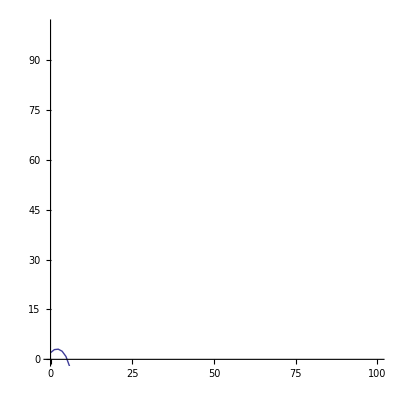

```mathematica
myplot1 = ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,200},PlotRange->{{0,100},{0,100}}]
Manipulate[g=9.8 (*m/s^2*);
Module[{sol=NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]),x[0]==0,y[0]==h,x'[0]==v*Cos[th],y'[0]==v*Sin[th]},{x,y},{t,0,tf}]},ParametricPlot[{{v Cos[th] t,h+v Sin[th] t-(1/2) g t^2},{Evaluate[{x[t],y[t]}/.sol]}},{t,0,tf},PlotRange->{{0,100},{0,100}},AxesLabel->{"x (m)","y (m)"},ImageSize->{500,300}]] ,{{tf,0.01,"time(s)"},0.01,10,Appearance->"Labeled"},{{v,10,"Velocity(m/s)"},0.01,100,Appearance->"Labeled"},{{vt,10,"Terminal Velocity(m/s)"},1.0,200,Appearance->"Labeled"},{{h,0,"Starting Height(m)"},0.0,5,Appearance->"Labeled"},{{th,50 Pi/180,"θ(rad/s)"},0.01,π,Appearance->"Labeled"}]
```

```mathematica
Manipulate[g=9.8 (*m/s^2*);
Module[ParametricPlot[{v Cos[th] t,h+v Sin[th] t-(1/2) g t^2},{t,0,tf},PlotRange->{{0,100},{0,100}},AxesLabel->{"x (m)","y (m)"},ImageSize->{500,300}]],{{tf,0.01,"time(s)"},0.01,10,Appearance->"Labeled"},{{v,10,"Velocity(m/s)"},0.01,100,Appearance->"Labeled"},{{vt,10,"Terminal Velocity(m/s)"},1.0,200,Appearance->"Labeled"},{{h,0,"Starting Height(m)"},0.0,5,Appearance->"Labeled"},{{th,50 Pi/180,"θ(rad/s)"},0.01,π,Appearance->"Labeled"}]
```

PART B)

Civil War Cannonball

```mathematica
c=.5;
rho=1.29;
Vter=√(2m*g/(C*rho*A));


Manipulate[g=9.8 (*m/s^2*);
Module[{sol=NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]),x[0]==0,y[0]==h,x'[0]==v*Cos[th],y'[0]==v*Sin[th]},{x,y},{t,0,tf}]},ParametricPlot[{{v Cos[th] t,h+v Sin[th] t-(1/2) g t^2},{Evaluate[{x[t],y[t]}/.sol]}},{t,0,tf},PlotRange->{{0,7500},{-10,500}},AxesLabel->{"x (m)","y (m)"},ImageSize->{500,300}]] ,{{tf,0.01,"time(s)"},0.01,100,Appearance->"Labeled"},{{v,10,"Velocity(m/s)"},0.01,500,Appearance->"Labeled"},{{vt,10,"Terminal Velocity(m/s)"},1.0,200,Appearance->"Labeled"},{{h,0,"Starting Height(m)"},0.0,5,Appearance->"Labeled"},{{th,50 Pi/180,"θ(rad/s)"},0.01,π,Appearance->"Labeled"}]
```

PART A)
Human

```mathematica
Manipulate[g=9.8 (*m/s^2*);
Module[{sol=NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]),x[0]==0,y[0]==h,x'[0]==v*Cos[th],y'[0]==v*Sin[th]},{x,y},{t,0,tf}]},ParametricPlot[{{v Cos[th] t,h+v Sin[th] t-(1/2) g t^2},{Evaluate[{x[t],y[t]}/.sol]}},{t,0,tf},PlotRange->{{0,100},{0,100}},AxesLabel->{"x (m)","y (m)"},ImageSize->{500,300}]] ,{{tf,0.01,"time(s)"},0.01,10,Appearance->"Labeled"},{{v,10,"Velocity(m/s)"},0.01,100,Appearance->"Labeled"},{{vt,10,"Terminal Velocity(m/s)"},1.0,200,Appearance->"Labeled"},{{h,0,"Starting Height(m)"},0.0,5,Appearance->"Labeled"},{{th,50 Pi/180,"θ(rad/s)"},0.01,π,Appearance->"Labeled"}]
```

Golf ball

```mathematica
Manipulate[g=9.8 (*m/s^2*);
Module[{sol=NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]),x[0]==0,y[0]==h,x'[0]==v*Cos[th],y'[0]==v*Sin[th]},{x,y},{t,0,tf}]},ParametricPlot[{{v Cos[th] t,h+v Sin[th] t-(1/2) g t^2},{Evaluate[{x[t],y[t]}/.sol]}},{t,0,tf},PlotRange->{{0,100},{0,100}},AxesLabel->{"x (m)","y (m)"},ImageSize->{500,300}]] ,{{tf,0.01,"time(s)"},0.01,10,Appearance->"Labeled"},{{v,10,"Velocity(m/s)"},0.01,100,Appearance->"Labeled"},{{vt,10,"Terminal Velocity(m/s)"},1.0,200,Appearance->"Labeled"},{{h,0,"Starting Height(m)"},0.0,5,Appearance->"Labeled"},{{th,50 Pi/180,"θ(rad/s)"},0.01,π,Appearance->"Labeled"}]
```

Baseball

```mathematica
Manipulate[g=9.8 (*m/s^2*);
Module[{sol=NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]),x[0]==0,y[0]==h,x'[0]==v*Cos[th],y'[0]==v*Sin[th]},{x,y},{t,0,tf}]},ParametricPlot[{{v Cos[th] t,h+v Sin[th] t-(1/2) g t^2},{Evaluate[{x[t],y[t]}/.sol]}},{t,0,tf},PlotRange->{{0,100},{0,100}},AxesLabel->{"x (m)","y (m)"},ImageSize->{500,300}]] ,{{tf,0.01,"time(s)"},0.01,10,Appearance->"Labeled"},{{v,10,"Velocity(m/s)"},0.01,100,Appearance->"Labeled"},{{vt,10,"Terminal Velocity(m/s)"},1.0,200,Appearance->"Labeled"},{{h,0,"Starting Height(m)"},0.0,5,Appearance->"Labeled"},{{th,50 Pi/180,"θ(rad/s)"},0.01,π,Appearance->"Labeled"}]
```

PART C)

```mathematica
Manipulate[g=9.8 (*m/s^2*);
Module[{sol=NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]),x[0]==0,y[0]==h,x'[0]==v*Cos[th],y'[0]==v*Sin[th]},{x,y},{t,0,tf}]},ParametricPlot[{{v Cos[th] t,h+v Sin[th] t-(1/2) g t^2},{Evaluate[{x[t],y[t]}/.sol]}},{t,0,tf},PlotRange->{{0,7500},{-10,500}},AxesLabel->{"x (m)","y (m)"},ImageSize->{500,300}]] ,{{tf,0.01,"time(s)"},0.01,100,Appearance->"Labeled"},{{v,10,"Velocity(m/s)"},0.01,500,Appearance->"Labeled"},{{vt,10,"Terminal Velocity(m/s)"},1.0,200,Appearance->"Labeled"},{{h,0,"Starting Height(m)"},0.0,5,Appearance->"Labeled"},{{th,50 Pi/180,"θ(rad/s)"},0.01,π,Appearance->"Labeled"}]
```

Note: part c is wrong since Mathematica is acting up. This was never fixed since Office Hours.